# Visualizing Data

```mathematica
{1,4,9,16,25}
```

{1,4,9,16,25}

```mathematica
data = %
```

{1,4,9,16,25}

```mathematica
data
```

{1,4,9,16,25}

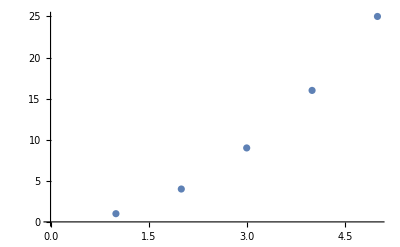

```mathematica
ListPlot[data]
```

WolframAlphaQueryParseResults

-Graphics-

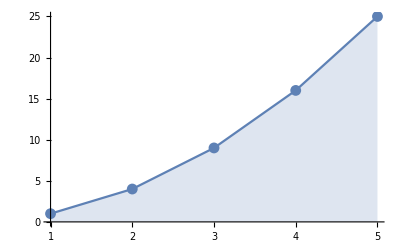

```mathematica
ListLinePlot[data, Mesh->All,
Filling->Axis,
AxesOrigin->{1,0}]
```

```mathematica
Manipulate[
lplot[data],
{lplot, {ListPlot,ListLinePlot,ListLogPlot,ListLogLogPlot}},
Initialization:>(data)]
```

ListPlot::lpn: data is not a list of numbers or pairs of numbers.

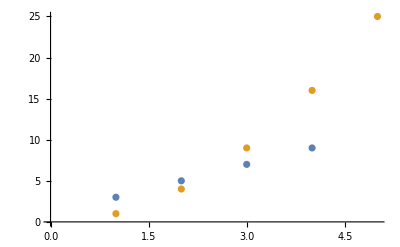

```mathematica
ListPlot[{{3,5,7,9},{1,4,9,16,25}}]
```

```mathematica
dataset1 = {1,4,9,16,25}
```

{1,4,9,16,25}

```mathematica
dataset2 = {3,5,7,8}
dataset3 = {2,5,9,14,20}
```

{3,5,7,8}

{2,5,9,14,20}

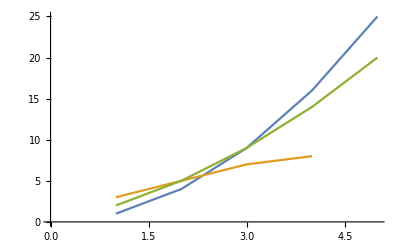

```mathematica
ListLinePlot[{dataset1,dataset2,dataset3}]
```

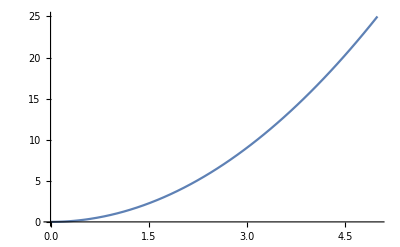

```mathematica
Plot[x^2,{x,0,5}]
```

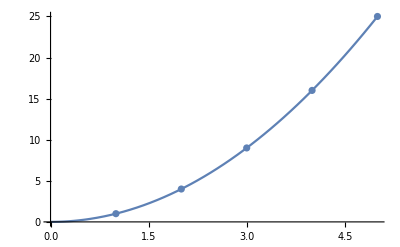

```mathematica
Show[Plot[x^2,{x,0,5}],ListPlot[{1,4,9,16,25}]]
```

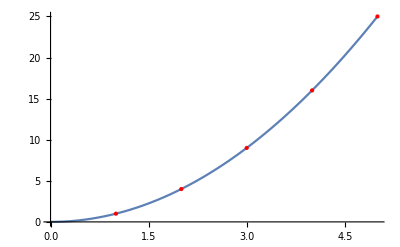

```mathematica
Show[Plot[x^2,{x,0,5}],ListPlot[{1,4,9,16,25},
PlotStyle->{Red,PointSize[Medium]}]]
```

```mathematica
ListPlot[{1,4,9,16,25}]
```

-Graphics-

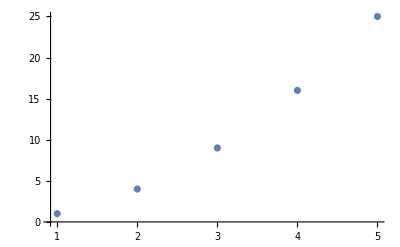

```mathematica
ListPlot[{{1,1},{2,4},{3,9},{4,16},{5,25}}]
```

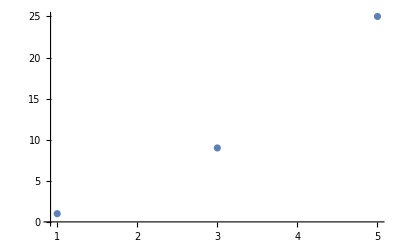

```mathematica
ListPlot[{{1,1},{3,9},{5,25}}]
```

```mathematica
ListPlot[{{3,9},{1,1},{5,25}}]
```

-Graphics-

```mathematica
dataset1={{1,1},{2,4},{3,9},{4,16},{5,25}};dataset2={{1,3},{2,5},{3,7},{4,9}};dataset3={{1,2},{2,5},{3,9},{4,14},{5,20}};
```

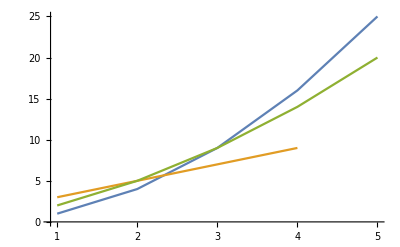

```mathematica
ListLinePlot[{dataset1,dataset2, dataset3}]
```

```mathematica
dataset4 = {100,12,24,46}
```

{100,12,24,46}

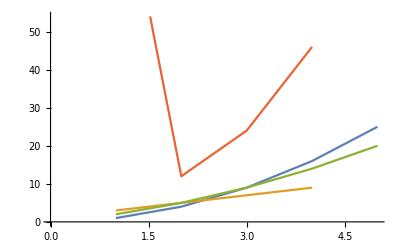

{1,2,3,5}

```mathematica
ListLinePlot[{dataset1,dataset2,dataset3,dataset4}]
```

```mathematica
Table[Prime[n],{n,5}]
```

{2,3,5,7,11}

```mathematica
Manipulate[
ListLinePlot[Table[{n,Prime[n]},{n,1,max,1}],PlotRange->{{0,50},{0,250}}],
{max,1,50,1}]
```

## Visualize a Three-Dimensional List of Numbers

```mathematica
data3 = Table[N[Sin[x]Cos[y]],
{x,-3,3,0.1},
{y,-3,3,.1}];
```

```mathematica
ListPlot3D[data3]
```

-Graphics3D-

```mathematica
ListPointPlot3D[data3]
```

-Graphics3D-

```mathematica
Manipulate[
func[Table[N[Sin[x]Cos[y], 10], {x,-3,3, incr},{y,-3,3}]],
{{incr, 1, "step size"}, 1, 0.05},
{{func,ListPlot3D, "function"}, {ListPlot3D,ListPointPlot3D}}]
```

## Visualize a Matrix

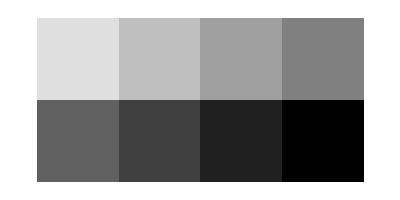

```mathematica
ArrayPlot[{{1,2,3,4},{5,6,7,8}}]
```

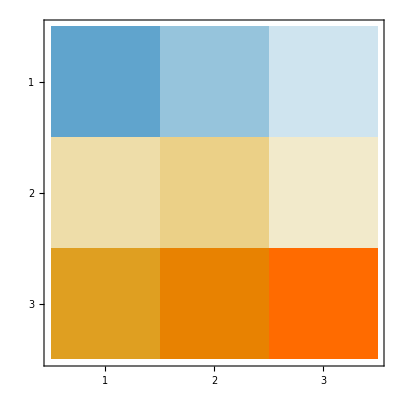

```mathematica
MatrixPlot[{{-10,-5,-1}, {2,4,0.1},{20,30,40}}]
```

### Magnitude vs. Sign Value

```mathematica
d = RandomInteger[{-100,100},{25,25}];
```

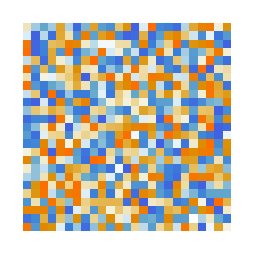
{-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[d,Frame->False],MatrixPlot[d, Frame->False]}
```

```mathematica
?Random*
```

```mathematica
RandomColor[3]
```

{RGBColor[0.25196344447706687, 0.49653910510675137, 0.6460481507165261],RGBColor[0.30492155288771206, 0.07173503014999572, 0.5372674929595147],RGBColor[0.6721776403008597, 0.8906332825294363, 0.38247423271320247]}

## Graphics related to Geography

```mathematica
GeoGraphics[{RandomColor[1],PointSize[Medium],Point[GeoPosition[{48.0862948,11.661045}]]}]
```

-Graphics-

```mathematica
GeoGraphics[{Red,PointSize[Medium],Point[GeoPosition[{48.0862948,11.661045}]]}]
```

-Graphics-

```mathematica
RandomColor[1]
```

{RGBColor[0.9570303344162401, 0.5919060257440301, 0.9474338136045397]}

```mathematica
GeoGraphics[{Red,PointSize[Large],Point[GeoPosition[{37.7699,-122.226}]],Point[GeoPosition[{37.2969,-121.819}]],Point[GeoPosition[{37.7599,-122.437}]]}]
```

-Graphics-

## Visualize Data With Charts

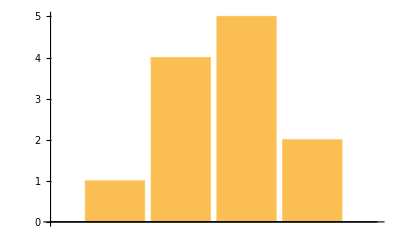

```mathematica
BarChart[{1,4,5,2}]
```

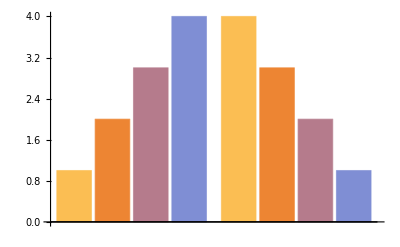

```mathematica
BarChart[{{1,2,3,4},{4,3,2,1}}]
```

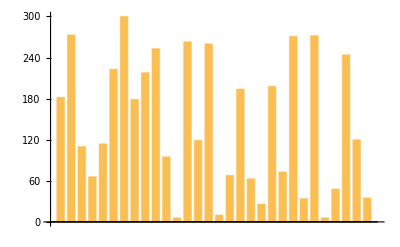

```mathematica
BarChart[RandomInteger[{1,300},30]]
```

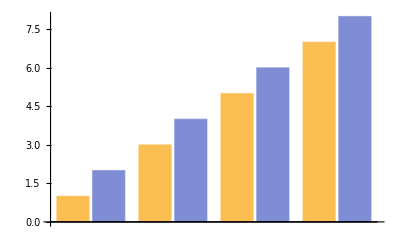

```mathematica
BarChart[{{1,2},{3,4},{5,6},{7,8}}]
```

```mathematica
Manipulate[
function[{{1,2},{3,4},{5,6},{7,8}}],
{function,{PieChart,PieChart3D,SectorChart,BarChart,BarChart3D}}]
```

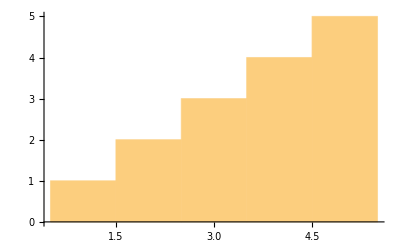

```mathematica
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5}]
```

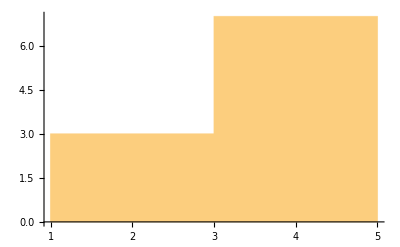

```mathematica
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5},{1,6,2}]
```

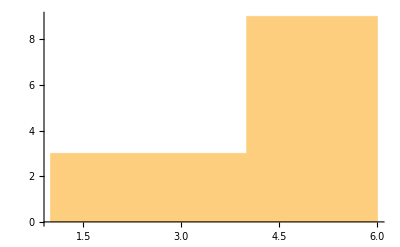

```mathematica
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5},{{1,3,4,6}}]
```

```mathematica
cloudNum = RandomInteger[{1,10},10]
```

{5,9,7,1,5,7,7,7,9,8}

```mathematica
WordCloud[cloudNum]
```

-Graphics-

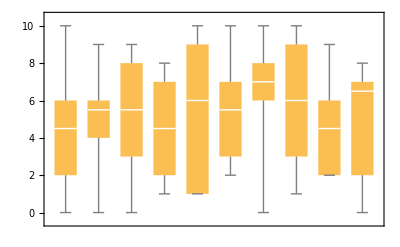

```mathematica
BoxWhiskerChart[RandomInteger[{0,10},{10,10}]]
```

```mathematica
Clear[data,dataset1,dataset2,dataset3,data3,d,cloudNum]
```

## Exercises

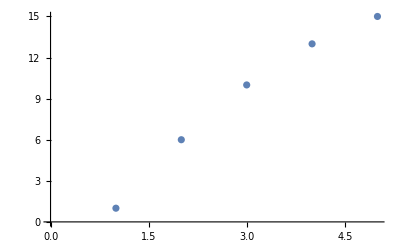

```mathematica
ListPlot[{1, 6, 10, 13, 15}]
```

```mathematica
ListPlot[{1, 6, 10, 13, 15},AxesOrigin->{0,0},Filling->None]
```

-Graphics-

```mathematica
res1 = {{0,0},{1,1},{2,3},{3,6},{5,15}};
res2 = {{0,3},{1,7},{2,10},{3,13},{4,15},{5,16}};
```

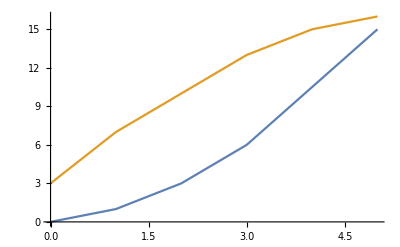

```mathematica
ListLinePlot[{res1,res2}]
```

```mathematica
Manipulate[
ListLinePlot[{{1,1},{2,i},{3,10}},
PlotRange->{0,11}],
{i,1,15}]
```

```mathematica
points17 = Table[i^3+i^2+1,{i,-50,50}];
```

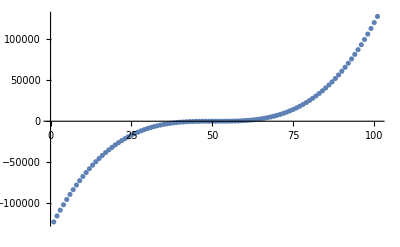

```mathematica
ListPlot[points17]
```

```mathematica
points21 = Table[Cos[a]+Sin[b],
{a,-10,10,.1},
{b,-10,10,.1}];
```

```mathematica
ListPlot3D[points21, Mesh->None]
```

-Graphics3D-

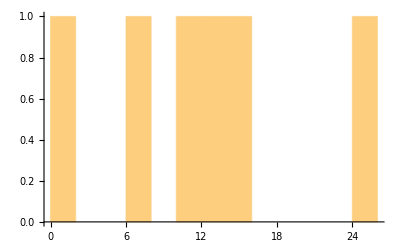

```mathematica
Histogram[{1,6,10,13,15,25},12]
```

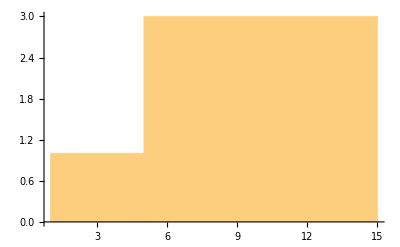

```mathematica
Histogram[{1,6,10,13,15,25},{{1,5,15}}]
```

```mathematica
Manipulate[
ThermometerGauge[6x,{0,20}],{x,1,3,.1}]
```